```mathematica
ClearAll["Global`*"]
H[a_]:=H0 Sqrt[Ωm/a^3];
Ψ[a_]:=-((3 H0^2 Ωm)/(2 a^3));

(*Solving perturbation equation for negligible and non-negilbile sound speed cases*)
ceff2[a_]:=0;
negligibleSolution=DSolve[a^2 H[a]^2 Δa''[a]+(3 a H[a]^2+a^2 H[a] H'[a]) Δa'[a]+(k^2 ceff2[a]/a^2+Ψ[a]) Δa[a]==0,Δa,a]//FullSimplify;
ceff2[a_]:=cs^2;
perturbedSolution=DSolve[a^2 H[a]^2 Δa''[a]+(3 a H[a]^2+a^2 H[a] H'[a]) Δa'[a]+(k^2 ceff2[a]/a^2+Ψ[a]) Δa[a]==0,Δa,a]//FullSimplify;
negligibleFunc=negligibleSolution[[1,1,2]];
perturbedFunc=Function[{a},(2/3)^(-1/6-1/6 √(25-(16 cs^2 k^2)/H0^2)) ((a^(3/2) k)/H0)^(-1/6-1/6 √(25-(16 cs^2 k^2)/H0^2)) C[1]+(3/2)^(1/6-1/6 √(25-(16 cs^2 k^2)/H0^2)) ((a^(3/2) k)/H0)^(-1/6+1/6 √(25-(16 cs^2 k^2)/H0^2)) C[2]];

(*Matching functions and derivatives at the start and end of the "kick"*)
solutionsForConstants1=Solve[{ai CC==perturbedFunc[ai],CC==D[perturbedFunc[a],a]/. a->ai},{C[1],C[2]}]//FullSimplify;
startKick =perturbedFunc /. {C[1]->solutionsForConstants1[[1,1,2]], C[2]->solutionsForConstants1[[1,2,2]]};
solutionsForConstants2=Solve[{(negligibleFunc[af])==(startKick[af]),(D[negligibleFunc[a],a]/. a->af)==(D[startKick[a],a]/. a->af)},{C[1],C[2]}]//Simplify;
endKick = negligibleFunc /. {C[1]->solutionsForConstants2[[1,1,2]], C[2]->solutionsForConstants2[[1,2,2]]};
Print["Completed."]
```

Completed.

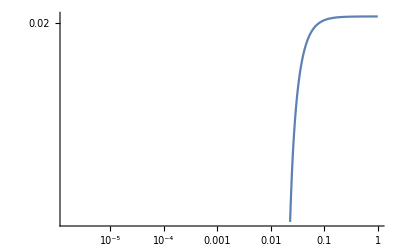

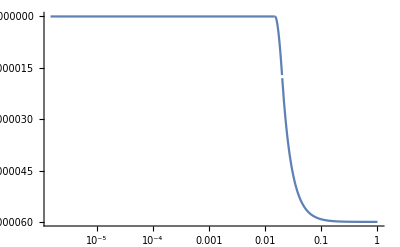

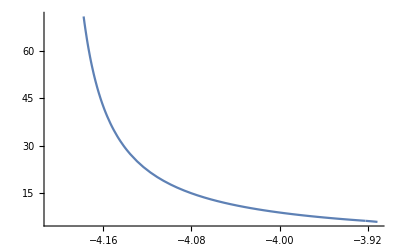

Completed.

```mathematica
(*Plotting*)
Clear[h,H0,Ωm,k,ai,af]
h=0.7; H0=0.0003335 h; Ωm=1; k=0.00528; ai=0.01489; af=0.020; da = Log[af/ai]; cs2want=0.0001;cs=√(cs2want/da);CC=1;
f[a_]:=-(CC a-δgdm[a])/(CC a );g[a_]:=-f[a];lg[a_]:=Log[g[a]];
δgdm[a_]:=Piecewise[{{CC a,a<ai},{startKick[a],ai≤ a≤ af}},endKick[a]];

LogLogPlot[{(CC a-δgdm[a])/(CC a )},{a,0.0001*ai,1}]
LogLinearPlot[(-δgdm[a]*Ψ[a]*a^2+CC*a*Ψ[a]*a^2)/k^2,{a,0.0001* ai,1}]
Plot[(lg[Exp[x+0.01]]-lg[Exp[x-.01]])/0.02,{x,Log[ai]-0.001,Log[af]+0.001}]
Print["Completed."]
```